# Analysis of the data obtained with VASP

León Ocaña^1, Yordan Solórzano^2, Luis Macas^1, Juan Diego Vizcaino^1

^1Group #2, School of Physical Science and Nanotechnology, Yachay Tech University, Urcuqui - Ecuador

## Part 1: The Si atom

Let' s analyze the results

```mathematica
wrkdir=
"\Users\LeDar\wrk\dft2024\part1_si_atom";
SetDirectory[wrkdir];
```

```mathematica
data1=Import["cell1.dat"];
data1//TableForm
```

4. | 0.682732
5. | 0.314767
6. | 0.0478779
7. | -0.0821132
8. | -0.134517
9. | -0.153991
10. | -0.160899
11. | -0.163289
12. | -0.164077

The following data was obtained with spin polarization in VASP (ISPIN=2)

```mathematica
data2=Import["cell.dat"];
data2//TableForm
```

4. | -0.187866
5. | -0.48054
6. | -0.70674
7. | -0.816868
8. | -0.860159
9. | -0.876066
10. | -0.881249
11. | -0.882925
12. | -0.88364

```mathematica
{data1, data2}//ListLinePlot[#,
Mesh->Full,
PlotMarkers->{Automatic, 8},
Frame->True,
FrameLabel->{"Cell Length (Å)", "Energy (eV)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotStyle->{{Red,Thick},{Blue,Thick}},
InterpolationOrder->2,
ImageSize->400,
Epilog->{Inset[
Panel[
Grid[{{"●","■"},{"ISPIN=1","ISPIN=2"}}//
Transpose//Map[Style[#,18]&,#,{2}]&]
],{Right,Top},{1.2,1.3}
]}]&
```

-Graphics-

## Part 2: The Cl^- ion

```mathematica
wrkdir=
"\Users\LeDar\wrk\dft2024\part2_cl_ion";
SetDirectory[wrkdir];
```

```mathematica
data1=Import["cell1.dat"];
data1//TableForm
```

4. | -2.52232
6. | -5.82899
8. | -5.93529
10. | -5.72529
12. | -5.51191
14. | -5.33306
16. | -5.18734

```mathematica
data2=Import["cell.dat"];
data2//TableForm
```

4. | -0.878292
6. | -3.65644
8. | -3.93381
10. | -3.97211
12. | -3.97904
14. | -3.98136
16. | -3.98286

```mathematica
{data1, data2}//ListLinePlot[#,
Mesh->Full,
PlotMarkers->{Automatic, 8},
Frame->True,
FrameLabel->{"Cell Length (Å)", "Energy (eV)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotStyle->{{Red,Thick},{Blue,Thick}},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Inset[
Panel[
Grid[{{"●","■"},{"No IDIPOL","IDIPOL=4"}}//
Transpose//Map[Style[#,18]&,#,{2}]&]
],{Right,Top},{1.2,1.3}
]}]&
```

-Graphics-

## Part 3: The Silicon Crystal

```mathematica
wrkdir=
"\Users\LeDar\wrk\dft2024\part3_silicon";
SetDirectory[wrkdir];
```

### Analysis of ENCUT

```mathematica
datasi = Import["ecut.dat"]//Map[#/{1,2}&,#]&
```

{{200,-5.92533},{250,-5.94026},{300,-5.94829},{350,-5.95047},{400,-5.95147},{450,-5.95163},{500,-5.95164},{550,-5.95169},{600,-5.95176},{650,-5.95181},{700,-5.95182},{750,-5.95182},{800,-5.95182},{850,-5.95184},{900,-5.95185}}

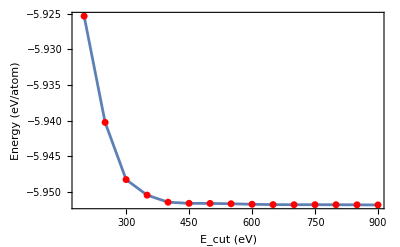

```mathematica
ListPlot[datasi,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datasi]}
]
```

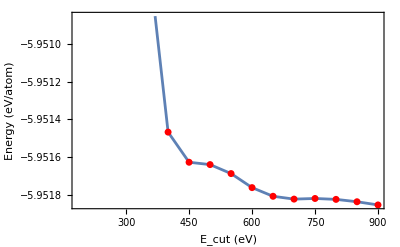

```mathematica
ListPlot[datasi,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->{-5.95185349,-5.95185349+10^-3},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datasi]}
]
```

### Analysis of k - points

```mathematica
datakp = Import["kps.dat"]//Map[#/{1,2}&,#]&
```

{{3,-5.63543},{4,-5.85444},{5,-5.91801},{6,-5.93916},{7,-5.94678},{8,-5.94976},{9,-5.95096},{10,-5.95151},{11,-5.9517},{12,-5.95181}}

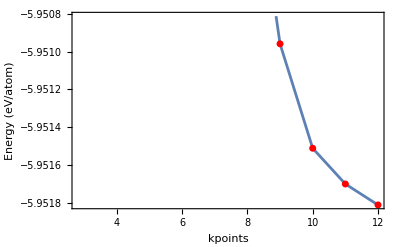

```mathematica
ListPlot[datakp,
Frame->True,
FrameLabel->{"kpoints","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->{-5.951811965,-5.951811965+10^-3},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datakp]}
]
```

For the k points grid we will use 9x9x9 to converge the energy to <1meV/atom

We know that for any crystal shape, the volume can be computed like:

```mathematica
a1 = a{1/2,1/2,0};
a2 = a{0,1/2,1/2};
a3= a{1/2,0,1/2};
a1.(a2 ×a3)
```

a^3/4

```mathematica
cell= Import["cell.dat"]//Map[{1/4(#[[1]])^3,#[[2]]}&,#]&
```

{{36.7995,-11.8576},{37.2192,-11.876},{37.6422,-11.8909},{38.0683,-11.9024},{38.4977,-11.9106},{38.9302,-11.9156},{39.366,-11.9176},{39.805,-11.9166},{40.2473,-11.9128},{40.6928,-11.9062},{41.1416,-11.897},{41.5938,-11.8852},{42.0492,-11.871},{42.5079,-11.8544}}

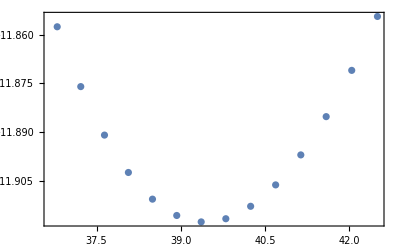

```mathematica
cell//ListPlot[#,Frame->True]&
```

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2(6-4((v0/v)^(2/3))));
```

```mathematica
NonlinearModelFit[cell,eos,{e0,v0,B0,B0'},v]
```

NonlinearModelFit::nrlnum: The function value {8.22051+0.0000174035 ⅈ,8.2389+0.0000172738 ⅈ,8.25381+0.0000171457 ⅈ,«6»,8.26912+0.0000162869 ⅈ,«4»} is not a list of real numbers with dimensions {14} at {e0,v0,B0,B0'} = {-3.63406,-0.0253016,0.224435,5.06106}.

FittedModel[-3.63406-0.0031942 ((6-0.34474 («1»)^(«1»)) «1»+«1»)]

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
```

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[11.343+5426.79/v^2+(«18»)/v^(4/3)-498.57/v^(2/3)]

```mathematica
nlm[v]
```

11.343+5426.79/v^2+2185.64/v^(4/3)-498.57/v^(2/3)

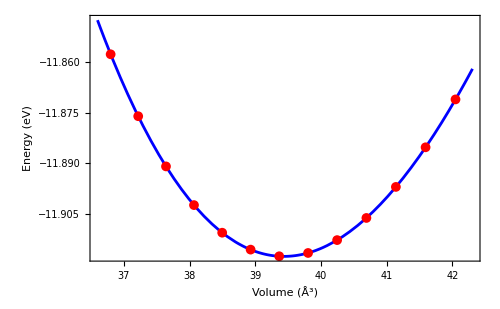

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2,(cell[[All,1]]//Max)-0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}
]
```

```mathematica
nlm["RSquared"]
```

1.

```mathematica
opVol=FindMinimum[nlm[v],
{v,39.5}]
```

{-11.9176,{v→39.4369}}

Bulk modulus

```mathematica
B0=v D[nlm[v],{v,2}]/.opVol[[2]]//UnitConvert[
Quantity[#,("Electronvolts")/("Angstroms")^3],
"GigaPascals"]&(*Converting to GigaPascals as the original units are eV/Å^3*)
```

96.5998 GPa

```mathematica
B0=v D[nlm[v],{v,2}]/.opVol[[2]];
B0'=-v/B0 D[v D[nlm[v],{v,2}],v]/.opVol[[2]](*Bulk Modulus pressure derivative*)
```

```mathematica
4.260882620220651(*Adimentional*)
```

Other way to get the mechanical properties of a crystal from the EOS.

```mathematica
nlm["BestFitParameters"]
```

{k[1]→11.343,k[2]→-498.57,k[3]→2185.64,k[4]→5426.79}

```mathematica
Clear[B0]
```

```mathematica
sol=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-11.9176,B0→0.602929,v0→39.4369,B'→4.26088}}

```mathematica
Solve[v0==a0^3/4,a0]/.sol
```

{{{a0→-2.70162+4.67934 ⅈ},{a0→5.40324},{a0→-2.70162-4.67934 ⅈ}}}

## Part: 4 The Silicon Crystal, functionals

```mathematica
wrkdir = "~/wrk/dft+2024/part4_silicon2";
```

```mathematica
SetDirectory[wrkdir];
```

### Results using PAW - PBE

```mathematica
cell  = Import["cell-pbe.dat"]// Map[{1/4(#[[1]])^3, #[[2]]}&, #]&
```

{{39.366,-10.8312},{39.366,-10.8312},{39.805,-10.8397},{40.2473,-10.8452},{40.4697,-10.8469},{40.6928,-10.8478},{40.9168,-10.8481},{41.1416,-10.8477},{41.3673,-10.8466},{41.5938,-10.8448},{42.0492,-10.8394},{42.5079,-10.8315}}

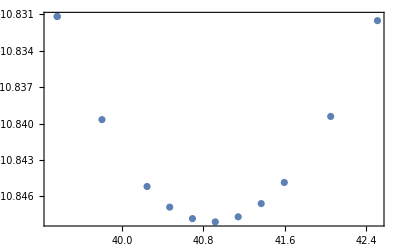

```mathematica
cell //ListPlot[#, Frame-> True]&
```

```mathematica
model  = k[1]+ k[2] v^(-2/3) + k[3] v^(-4/3) + k[4] v^2;
```

```mathematica
parameters = Table[k[i], {i, 4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm = NonlinearModelFit[cell, model, parameters,v]
```

FittedModel[18.7423+3942.75/v^(4/3)-678.64/v^(2/3)-0.000239726 v^2]

```mathematica
nlm[v]
```

18.7423+3942.75/v^(4/3)-678.64/v^(2/3)-0.000239726 v^2

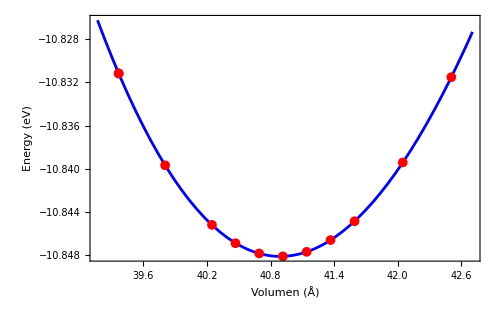

```mathematica
Plot[nlm[v],{v, (cell[[All, 1]]//Min)-0.2,
(cell[[All,1]]//Max )+0.2},
Frame->True,
FrameLabel->{"Volumen (Å)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica", FontSize-> 19},
ImageSize->500,
PlotRange->All,
Epilog-> {
AbsolutePointSize[7], Red, Point[cell]}
]
```

```mathematica
nlm["RSquared"]
```

1.

```mathematica
opVol = FindMinimum[nlm[v],{v, 41.1} ]
```

{-10.8481,{v→40.8915}}

Bulk Modulus units eV/[Å^3]== Force*Lengt/Length^3 = F/L^2 = Presure,
mean how difficult to deform a material por unit of area

```mathematica
B0 = v D[nlm[v], {v,2}]/.opVol[[2]]//UnitConvert[Quantity[#, "Electronvolts"/("Angstroms")^3],"GigaPascals"]&
```

89.0957 GPa

Transform to N / m^2 equal pressure Pascal

```mathematica
B0 = v D[nlm[v], {v,2}]/.opVol[[2]]; (*bulk  in eV/Å^3*)
```

```mathematica
B0' = -v/B0 D[ v D[nlm[v], {v,2}], v]/.opVol[[2]]  (*Undimensionless*)
```

4.31339

Bulk pressuere derivate mean that high pressure can be harmless to deforms of B0', when is negative mean is a material soft and cannot done a harmeless deformation

Other way to get mechanicla properties of a crystal from the EOS equation

```mathematica
nlm["BestFitParameters"]
```

{k[1]→18.7423,k[2]→-678.64,k[3]→3942.75,k[4]→-0.000239726}

```mathematica
Clear[B0, v0]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+(27 B0 v0^(5/3) B')/16== k[2],
 (63 B0 v0^(7/3))/8-(27 B0 v0^(7/3) B')/16 ==k[3],
 -(9 B0 v0^3)/4+(9 B0 v0^3 B')/16==k[4]}/.nlm["BestFitParameters"], {e0,B0, v0, B'}]
```

{{e0→-10.4602,B0→0.655361,v0→39.6082,B'→4.}}

```mathematica
Solve[v0 ==  a0^3/4, a0]/.v0 ->40.8914
```

{{a0→-2.73443+4.73618 ⅈ},{a0→5.46887},{a0→-2.73443-4.73618 ⅈ}}

```mathematica
B0/.sol[[1]]// UnitConvert[Quantity[#, "Electronvolts"/("Angstroms")^3], "GigaPascals"]&
```

105. GPa

### Results using PAW - PBEsol

```mathematica
cell  = Import["cell-pbesol.dat"]// Map[{1/4(#[[1]])^3, #[[2]]}&, #]&
```

{{36.7995,-11.3962},{37.2192,-11.42},{37.6422,-11.4402},{38.0683,-11.4569},{38.4977,-11.4702},{38.9302,-11.4802},{39.366,-11.487},{39.805,-11.4908},{40.2473,-11.4917},{40.6928,-11.4897},{41.1416,-11.485},{41.5938,-11.4776},{42.0492,-11.4677},{42.5079,-11.4553},{42.9699,-11.4406},{43.4353,-11.4236},{43.904,-11.4044}}

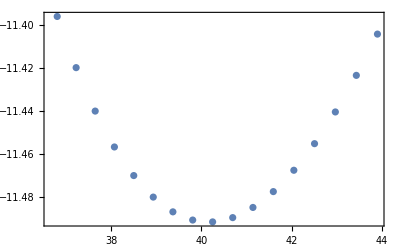

```mathematica
cell //ListPlot[#, Frame-> True]&
```

```mathematica
model  = k[1]+ k[2] v^(-2/3) + k[3] v^(-4/3) + k[4] v^2;
```

```mathematica
parameters = Table[k[i], {i, 4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm = NonlinearModelFit[cell, model, parameters,v]
```

FittedModel[18.2671+(«19»)/(«1»)-«1»-0.000207338 v^2]

```mathematica
nlm[v]
```

18.2671+3908.36/v^(4/3)-678.34/v^(2/3)-0.000207338 v^2

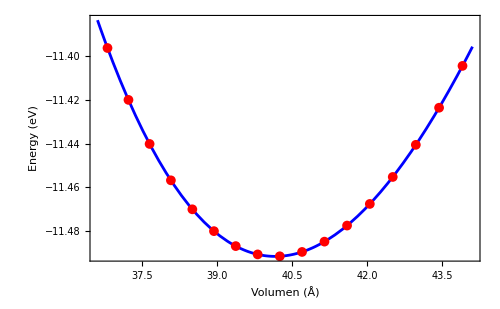

```mathematica
Plot[nlm[v],{v, (cell[[All, 1]]//Min)-0.2,
(cell[[All,1]]//Max )+0.2},
Frame->True,
FrameLabel->{"Volumen (Å)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica", FontSize-> 19},
ImageSize->500,
PlotRange->All,
Epilog-> {
AbsolutePointSize[7], Red, Point[cell]}
]
```

```mathematica
nlm["RSquared"]
```

1.

```mathematica
opVol = FindMinimum[nlm[v],{v, 41.1} ]
```

{-11.4917,{v→40.1571}}

Bulk Modulus units eV/[Å^3]== Force*Lengt/Length^3 = F/L^2 = Presure,
mean how difficult to deform a material por unit of area

```mathematica
B0 = v D[nlm[v], {v,2}]/.opVol[[2]]//UnitConvert[Quantity[#, "Electronvolts"/("Angstroms")^3],"GigaPascals"]&
```

93.681 GPa

Transform to N / m^2 equal pressure Pascal

```mathematica
B0 = v D[nlm[v], {v,2}]/.opVol[[2]]; (*bulk  in eV/Å^3*)
```

```mathematica
B0' = -v/B0 D[ v D[nlm[v], {v,2}], v]/.opVol[[2]]  (*Undimensionless*)
```

4.25315

Bulk pressuere derivate mean that high pressure can be harmless to deforms of B0', when is negative mean is a material soft and cannot done a harmeless deformation

Other way to get mechanicla properties of a crystal from the EOS equation

```mathematica
nlm["BestFitParameters"]
```

{k[1]→18.2671,k[2]→-678.34,k[3]→3908.36,k[4]→-0.000207338}

```mathematica
Clear[B0, v0]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+(27 B0 v0^(5/3) B')/16== k[2],
 (63 B0 v0^(7/3))/8-(27 B0 v0^(7/3) B')/16 ==k[3],
 -(9 B0 v0^3)/4+(9 B0 v0^3 B')/16==k[4]}/.nlm["BestFitParameters"], {e0,B0, v0, B'}]
```

{{e0→-11.1662,B0→0.668836,v0→39.1171,B'→4.}}

```mathematica
Solve[v0 ==  a0^3/4, a0]/.v0 ->40.8914
```

{{a0→-2.73443+4.73618 ⅈ},{a0→5.46887},{a0→-2.73443-4.73618 ⅈ}}

```mathematica
B0/.sol[[1]]// UnitConvert[Quantity[#, "Electronvolts"/("Angstroms")^3], "GigaPascals"]&
```

107.159 GPa

## Part 5: The silicon crystal using PBE

```mathematica
wrkdir=
"\Users\LeDar\wrk\dft2024\part5_silicon3";
SetDirectory[wrkdir];
```

Syntax::stresc: Unknown string escape \U.

Syntax::stresc: Unknown string escape \L.

Syntax::stresc: Unknown string escape \w.

Syntax::stresc: Unknown string escape \d.

Syntax::stresc: Unknown string escape \p.

The cohesion energy in [eV/atom] for Silicon fcc is

```mathematica
e[bulk]/n-e[atom]/.{e[bulk]->-10.84807047,
e[atom]->-0.88363161,n->2}
```

-4.5404

Please comment this results considering the experimental value of -4.62±0.08 [eV/atom].

### The density of states (DOS) and partial density of states (PDOS)

```mathematica
input=Import["DOSCAR","Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

5.66955

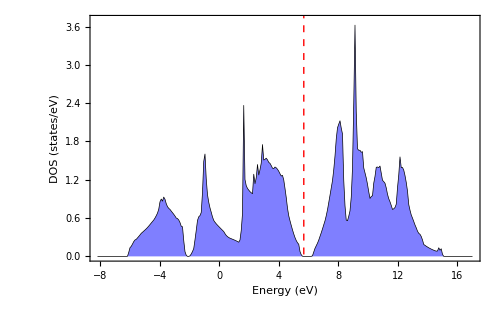

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{All,{0,3.7}}]
```

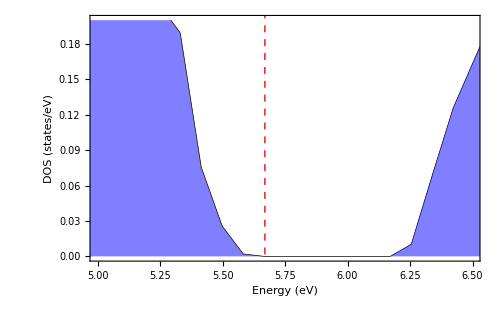

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{{5,6.5},{0,0.2}}]
```

```mathematica
ef-6.1700898070959695
```

-0.500537

Let' s integrate the DOS from - 8.2 to Ef

```mathematica
interp=Interpolation[dos]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[interp[x],{x,-8.2,ef}]
```

InterpolatingFunction::dmvali: The integration endpoint -8.2 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

8.05949

Now we are going to analyze the PDOS, we have to consider this:

energy s p_y p_z p_x d_ {xy} d_ {yz} d_ {z2 - r2} d_ {xz} d_ {x2 - y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
dos2=input[[7+300+2+300+2;;7+300+2+300+2+300]];
```

```mathematica
dosall=(dos1+dos2)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

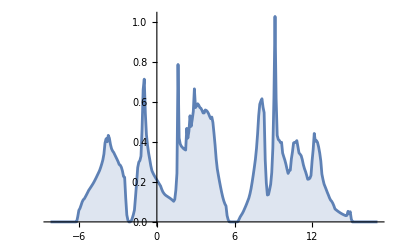

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,
#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
dosall//f[total]//
ListPlot[#,Joined->True,Filling->Axis]&
```

The s-states will be

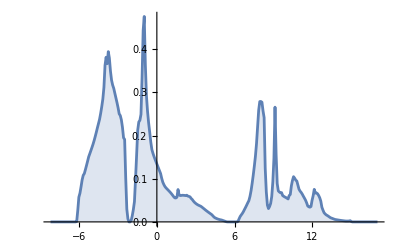

```mathematica
dosall//f[s]//
ListPlot[#,Joined->True,Filling->Axis]&
```

For p-states

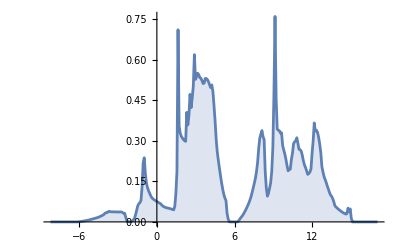

```mathematica
dosall//f[p]//
ListPlot[#,Joined->True,Filling->Axis]&
```

For d-states

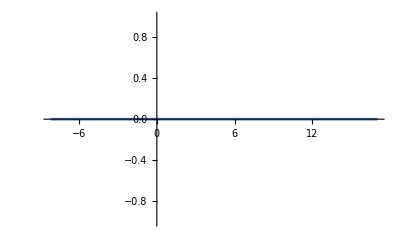

```mathematica
dosall//f[d]//
ListPlot[#,Joined->True,Filling->Axis]&
```

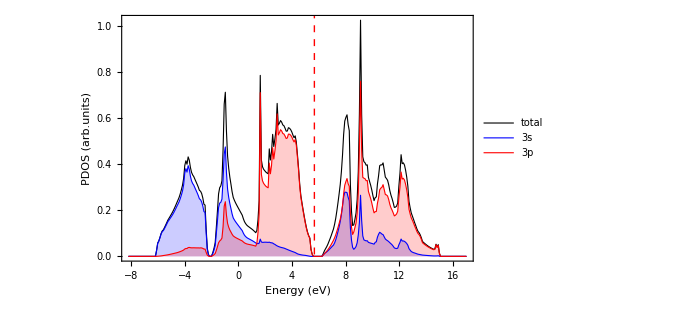

```mathematica
{dosall//f[total],dosall//f[s],dosall//f[p]}//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis},
Frame->True,
FrameLabel->{"Energy (eV)","PDOS (arb.units)"},
PlotRange->All,
PlotLegends->Placed[{"total","3s","3p"},{Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->
Directive[Red, Dashed,
AbsoluteThickness[1.0]],
PlotStyle->
{{AbsoluteThickness[0.8],Black}, 
{AbsoluteThickness[0.8],Blue},
{AbsoluteThickness[0.8],Red}},
BaseStyle->{FontFamily->"Helvetica", 
FontSize->18}
]&
```

### The band structure of Si - FCC using PROCAR_OPT file

%%%% you can run the lines below %%%%%%%%%

```mathematica
(*Run["grep k-point PROCAR_OPT > kpt"];
Run["sed 's/-/ -/g' kpt > kpt2"];
Run["sed 's/k -point/k-point/g' kpt2 > kpts"];
Run["rm kpt kpt2"];
Run["grep band PROCAR_OPT > bandData"];
Run["grep \"# of bands\" PROCAR_OPT | tail -1 > numbands"];*)
```

```mathematica
(*define the Fermi elevel take from previous calculations*)
ef =input[[6,4]]
```

5.66955

```mathematica
(*ef=input[[6,4]];*)
```

```mathematica
(*This gets number of kp and bands*)
bandsinfo=Import["numbands","Table"][[1]];
{Nkpt,Nbands}=bandsinfo//{#[[4]],#[[8]]}&
```

{140,8}

```mathematica
(*This gets the high symmetry points and divisions*)
path=Import["KPOINTS-bs","Table"];
div=path[[2,1]];
```

```mathematica
(*This defines the high symmetry points labels and the length*)
hsympts=(If[(path[[5]]//Length)==4,path[[5;;-1]]//Flatten//Partition[#,4]&//#[[All,4]]&, path[[5;;-1]]//Flatten//Partition[#,5]&//#[[All,5]]&]//Drop[#,{3,Length[#],2}]&)/."GAMMA"->"Γ"
NumGridL=(hsympts//Length)-2;
```

{L,Γ,X,K,Γ}

```mathematica
(*This defines the band energies shifted to Ef*)
bands=Import["bandData","Table"][[2;;-1]][[All,5]]-ef//Partition[#,Nbands]&;
bandener=bands//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This defines k-point coordinates*)
kp=Import["kpts","Table"][[2;;-1]][[All,{4,5,6}]];
kpt=kp//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This liniarizes k-point coordinates in 1D*)
kpt2=Join[{0},Table[Norm[kpt[[i+1]]-kpt[[i]]],{i,(kpt//Length)-1}]]//Accumulate;
```

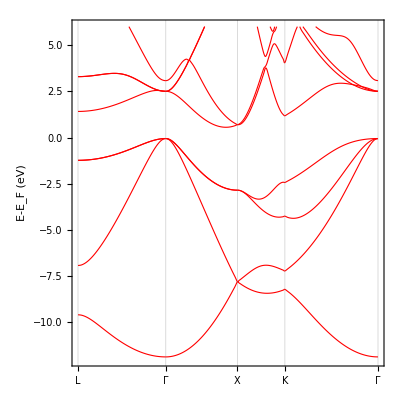

```mathematica
(*This creates the bands in kpt2 domain*)
bands2={kpt2,bandener}//Transpose;
Do[bd[i]=bands2//Map[{#[[1]],#[[2,i]]}&,#]&,{i,Nbands}];

(*please provide the bands you want to plot*)
ListPlot[Table[bd[i],{i,1,8(*Nbands*)}],
Frame->True,
FrameLabel->{"","E-E_F (eV)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->14},
Joined->True,
InterpolationOrder->2,
AspectRatio->1,
AxesStyle->Directive[Black,Dashed, AbsoluteThickness[0.7]],
FrameTicks->{{Automatic,None},{{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],hsympts}//Transpose,None}},
GridLines->{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],None},
PlotStyle->Directive[Red,AbsoluteThickness[0.8]],
PlotRange->{{0,kpt2[[-1]]},{-12,6}}]
```

```mathematica
int5=Interpolation[bd[5]]
```

InterpolatingFunction[…]

```mathematica
FindMinimum[int5[x],x]
```

{0.556632,{x→1.45916}}

The band gap E_g for Si-FCC using PAW - PBE is predicted to be 0.56 eV

### Visualization of the CHGCAR.vasp

In the following figure, we display the iso-density of the valence electrons. Notice the distribution.

In the following figure, we display the contour plot of the electronic density. Notice the distribution .

## Part 6 : The Silicon crystal phases

```mathematica
wrkdir=
"/Users/LeDar/wrk/dft2024/part6_silicon4/results";
SetDirectory[wrkdir];
```

### Analysis of ENCUT

```mathematica
datasi = Import["ecut.dat"]//Map[#/{1,2}&,#]&
```

{{250,-5.122},{300,-5.12875},{350,-5.13232},{400,-5.13366},{450,-5.13391},{500,-5.13394},{550,-5.13397},{600,-5.13404},{650,-5.13406},{700,-5.13406},{750,-5.13405},{800,-5.13404},{850,-5.13404},{900,-5.13404}}

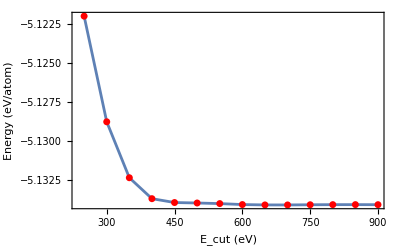

```mathematica
ListPlot[datasi,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datasi]}
]
```

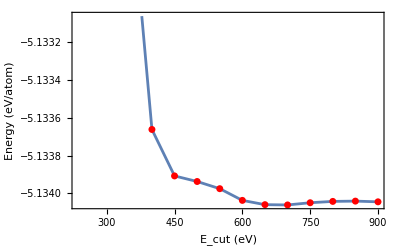

```mathematica
ListPlot[datasi,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->{datasi[[10,2]],datasi[[10,2]]+10^-3},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datasi]}
]
```

Then we use ENCUT=400

### Analysis of k - points

```mathematica
datakp = Import["kps.dat"][[All,{1,2}]]//Map[#/{1,2}&,#]&
```

{{0.29531,-5.1346},{0.270177,-5.13462},{0.257611,-5.13366},{0.245044,-5.13366},{0.226195,-5.13425},{0.207345,-5.13372},{0.201062,-5.13286},{0.182212,-5.13357},{0.175929,-5.13349},{0.163363,-5.13314},{0.15708,-5.13336},{0.150796,-5.13347},{0.144513,-5.13328},{0.13823,-5.13303},{0.131947,-5.13328},{0.125664,-5.13314}}

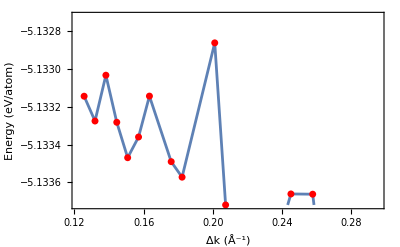

```mathematica
ListPlot[datakp,
Frame->True,
FrameLabel->{"Δk (Å^-1)","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->{datakp[[6,2]],datakp[[6,2]]+10^-3},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datakp]}
]
```

```mathematica
datakp[[6,1]]
```

0.207345

We use a Δk=0.207345 Å^-1 that corresponds to a grid of 13x13x9 to converge the energy to <1meV/atom

We know that for any crystal shape, the volume can be computed like:

```mathematica
a1 = a{1/2,1/2,0};
a2 = a{0,1/2,1/2};
a3= a{1/2,0,1/2};
a1.(a2 ×a3)
```

a^3/4

```mathematica
cell= Import["cell.dat"][[All,{1,2}]]
```

{{27.7,-10.1444},{28.2,-10.1839},{28.7,-10.2148},{29.2,-10.2378},{29.7,-10.2535},{30.2,-10.263},{30.7,-10.2674},{31.2,-10.265},{31.7,-10.2576},{32.2,-10.2456},{32.7,-10.2294},{33.2,-10.2094},{33.7,-10.186},{34.2,-10.1594},{34.7,-10.13}}

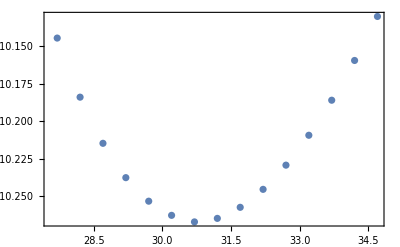

```mathematica
cell//ListPlot[#,Frame->True]&
```

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2(6-4((v0/v)^(2/3))));
```

```mathematica
NonlinearModelFit[cell,eos,{e0,v0,B0,B0'},v]
```

NonlinearModelFit::nrlnum: The function value {6.73729+0.000161967 ⅈ,6.77682+0.000160088 ⅈ,6.80769+0.000158263 ⅈ,6.83066+0.000156489 ⅈ,«4»,6.85051+0.000148315 ⅈ,6.83849+0.000146806 ⅈ,«5»} is not a list of real numbers with dimensions {15} at {e0,v0,B0,B0'} = {-3.39696,-0.0757357,0.239553,5.01412}.

FittedModel[-3.39696-0.0102053 ((6-0.716023 (-1/v)^(2/3)) (-1+«19» «1»)^2+5.01412 «1»)]

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
```

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[8.7921+3930.37/v^2+1035.32/v^(4/3)-333.345/v^(2/3)]

```mathematica
nlm[v]
```

8.7921+3930.37/v^2+1035.32/v^(4/3)-333.345/v^(2/3)

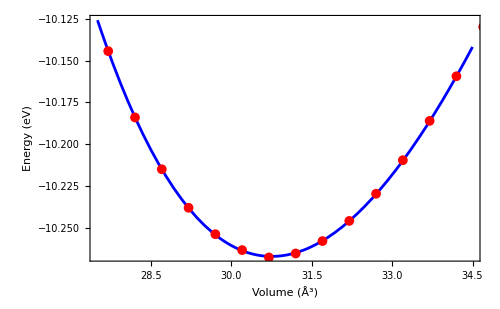

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2,(cell[[All,1]]//Max)-0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}
]
```

```mathematica
nlm["RSquared"]
```

1.

```mathematica
opVol=FindMinimum[nlm[v],
{v,31}]
```

{-10.2667,{v→30.7513}}

Bulk modulus

```mathematica
B0=v D[nlm[v],{v,2}]/.opVol[[2]]//UnitConvert[
Quantity[#,("Electronvolts")/("Angstroms")^3],
"GigaPascals"]&(*Converting to GigaPascals as the original units are eV/Å^3*)
```

107.514 GPa

```mathematica
B0=v D[nlm[v],{v,2}]/.opVol[[2]];
B0'=-v/B0 D[v D[nlm[v],{v,2}],v]/.opVol[[2]](*Bulk Modulus pressure derivative*)
```

4.35807

Other way to get the mechanical properties of a crystal from the EOS.

```mathematica
nlm["BestFitParameters"]
```

{k[1]→8.7921,k[2]→-333.345,k[3]→1035.32,k[4]→3930.37}

```mathematica
Clear[B0]
```

```mathematica
sol=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-10.2667,B0→0.671051,v0→30.7513,B'→4.35807}}

```mathematica
Solve[v0==a0^3/4,a0]/.sol
```

{{{a0→-2.48663+4.30697 ⅈ},{a0→4.97326},{a0→-2.48663-4.30697 ⅈ}}}

### The density of states (DOS) and partial density of states (PDOS)

```mathematica
input=Import["DOSCAR-bulk","Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

9.03195

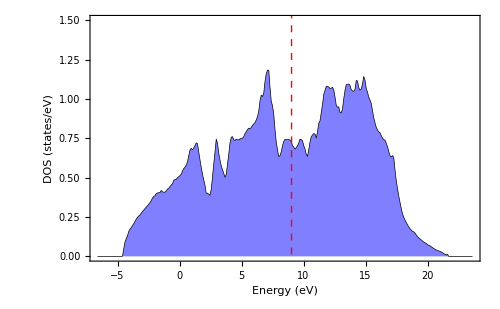

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{All,{0,1.5}}]
```

From this result, this Silicon phase is metallic.

Let' s integrate the DOS from - 6 to Ef

```mathematica
interp=Interpolation[dos]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[interp[x],{x,-6,ef}]
```

7.99971

Now we are going to analyze the PDOS, we have to consider this:

energy s p_y p_z p_x d_ {xy} d_ {yz} d_ {z2 - r2} d_ {xz} d_ {x2 - y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
dos2=input[[7+300+2+300+2;;7+300+2+300+2+300]];
```

```mathematica
dosall=(dos1+dos2)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

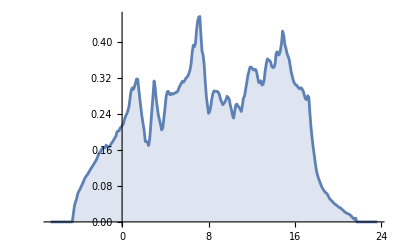

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,
#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
dosall//f[total]//
ListPlot[#,Joined->True,Filling->Axis]&
```

The s-states will be

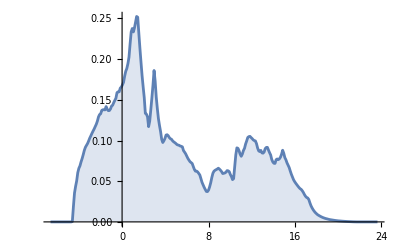

```mathematica
dosall//f[s]//
ListPlot[#,Joined->True,Filling->Axis]&
```

For p-states

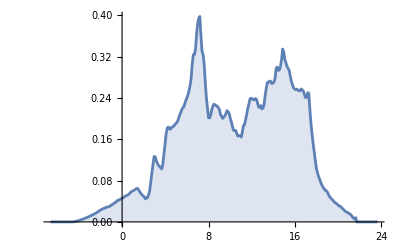

```mathematica
dosall//f[p]//
ListPlot[#,Joined->True,Filling->Axis]&
```

For d-states

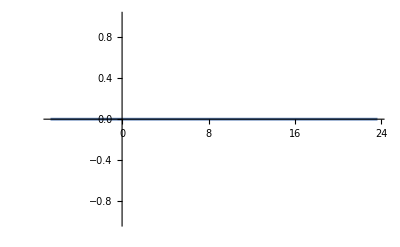

```mathematica
dosall//f[d]//
ListPlot[#,Joined->True,Filling->Axis]&
```

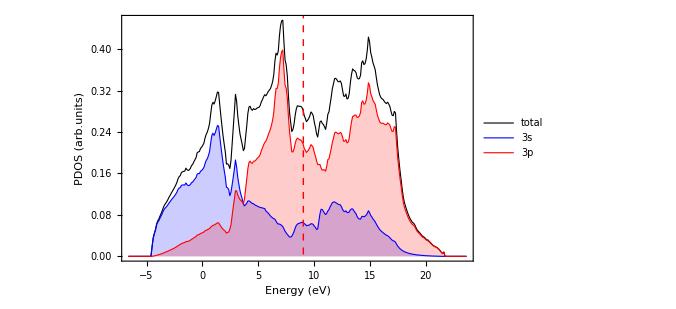

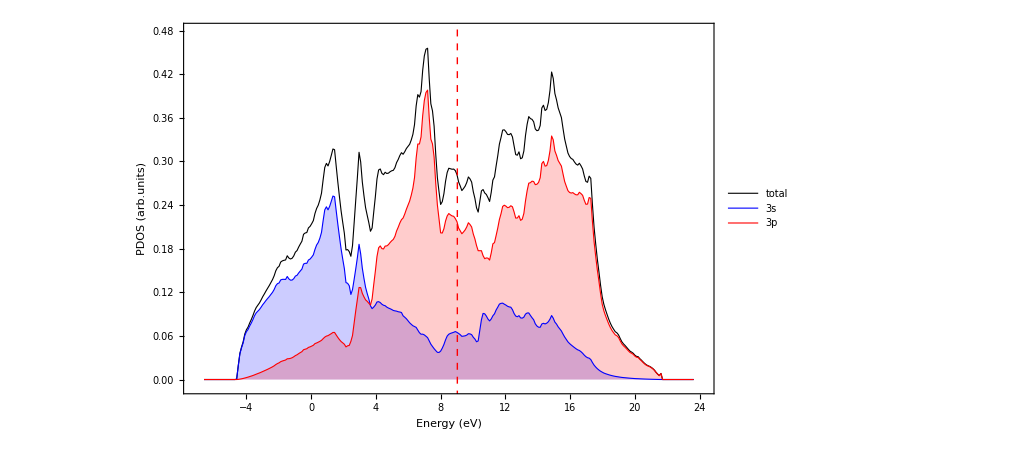

```mathematica
{dosall//f[total],dosall//f[s],dosall//f[p]}//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis},
Frame->True,
FrameLabel->{"Energy (eV)","PDOS (arb.units)"},
PlotRange->All,
PlotLegends->Placed[{"total","3s","3p"},{Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->
Directive[Red, Dashed,
AbsoluteThickness[1.0]],
PlotStyle->
{{AbsoluteThickness[0.8],Black}, 
{AbsoluteThickness[0.8],Blue},
{AbsoluteThickness[0.8],Red}},
BaseStyle->{FontFamily->"Helvetica", 
FontSize->18}
]&
```

The cohesion energy in [eV/atom] for silicon phase is:

```mathematica
e[bulk]/n-e[atom]/.{e[bulk]->-10.26738152,
e[atom]->-0.88363161,n->2}
```

-4.25006

### Visualization of the charge density

### Semiconductor VS metallic phases of Silicon

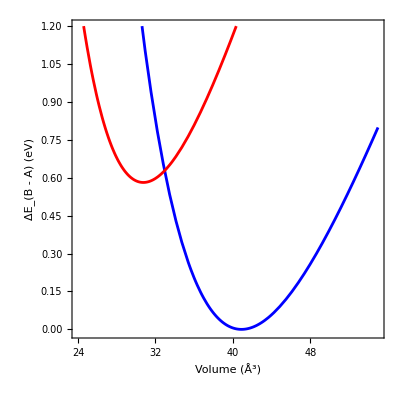

```mathematica
E227=-10.84807047;
EoS227[v_]:=10.677140018865446+6779.214666933382/v^2+1890.1190108267504/v^(4/3)-462.8542575206727/v^(2/3)-E227;
EoSmetal[v_]:=8.792101925077583+3930.367598521086/v^2+1035.3194146942258/v^(4/3)-333.3452547572423/v^(2/3)-E227;
Plot[{EoS227[v],EoSmetal[v],EoS227[70.50886937082902]},
{v,24,55},
Frame->True,
FrameLabel->{"Volume (Å^3)","ΔE_(B - A) (eV)"},
PlotRange->{-0.01,1.2},
AspectRatio->1,
PlotStyle->{Blue,Red}]
```

```mathematica
Clear[sol]
```

```mathematica
sol=FindRoot[{D[EoSmetal[v2],v2]==D[EoS227[v1],v1]==(EoSmetal[v2]-EoS227[v1])/(v2-v1)},{{v1,38},{v2,26}}]
```

{v1→37.3384,v2→28.4601}

```mathematica
m=D[EoSmetal[v2],v2]/.sol
```

-0.0615315

```mathematica
UnitConvert[Quantity[m,"Electronvolts"/("Angstroms")^3],"Gigapascals"]
```

-9.85843 GPa

```mathematica
line=Solve[(y-EoS227[v1])/(v-v1)==m/.sol,y]//FullSimplify
```

{{y→2.39828-0.0615315 v}}

```mathematica
Plot[{Callout[EoS227[v],"Sym A=227",{50,0.8}],Callout[EoSmetal[v],"Sym A=141",{39,0.6}],y/.line[[1]]},
{v,24,55},
Frame->True,
FrameLabel->{"Volume (Å^3)","ΔE_(B - A) (eV)"},
PlotRange->{-0.01,1.2},
AspectRatio->1,
PlotStyle->{Blue,Red,Black},
Epilog->{Green,AbsolutePointSize[6],Point[{{v1,EoS227[v1]},{v2,EoSmetal[v2]}}/.sol]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18}]
```

-Graphics-

## Part 7: The NiO oxide

```mathematica
wrkdir=
"/home/yor/wrk/dft+2024/part7_nio/part7_nio";
SetDirectory[wrkdir];
```

### The non - magnetic NM phase

```mathematica
cellnm=Import["cell-nm.dat"][[All,{1,2}]]
```

{{33.5,-22.6073},{34.,-22.6544},{34.5,-22.6892},{35.,-22.7128},{35.5,-22.7261},{36.,-22.7296},{36.5,-22.7243},{37.,-22.7106},{37.5,-22.6893},{38.,-22.661},{38.5,-22.6262},{39.,-22.5853},{35.9423,-22.7297},{35.9423,-22.7297}}

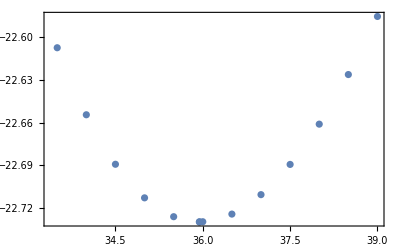

```mathematica
cellnm//ListPlot[#,Frame->True]&
```

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
```

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm=NonlinearModelFit[cellnm,model,parameters,v]
```

FittedModel[13.6919+20496.8/v^2+(«18»)/v^(4/3)-620.537/v^(2/3)]

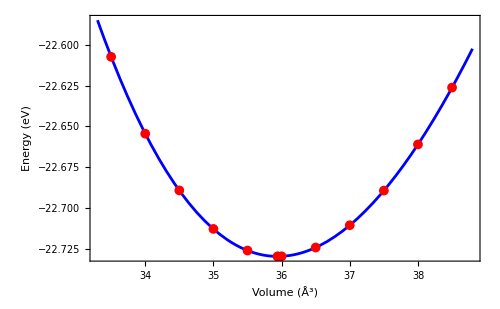

```mathematica
Plot[nlm[v],{v,(cellnm[[All,1]]//Min)-0.2,(cellnm[[All,1]]//Max)-0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cellnm]}
]
```

```mathematica
Clear[B0]
```

```mathematica
sol=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-22.7297,B0→1.29313,v0→35.9422,B'→4.60688}}

```mathematica
Solve[v0==a0^3/4,a0]/.sol
```

{{{a0→-2.61934+4.53683 ⅈ},{a0→5.23868},{a0→-2.61934-4.53683 ⅈ}}}

### The ferromagnetic FM phase

```mathematica
cellfm=Import["cell-fm.dat"][[All,{1,2}]]
```

{{34.,-22.6394},{34.5,-22.6767},{35.,-22.7047},{35.5,-22.7265},{36.,-22.7384},{36.5,-22.7414},{37.,-22.7444},{37.5,-22.7346},{38.,-22.7209},{38.5,-22.7009},{39.,-22.6754},{39.5,-22.6448},{36.6531,-22.7464}}

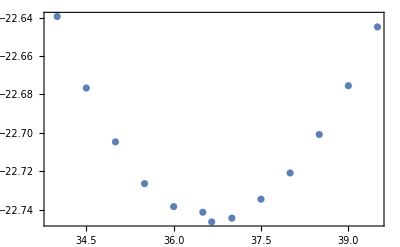

```mathematica
cellfm//ListPlot[#,Frame->True]&
```

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
```

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm=NonlinearModelFit[cellfm,model,parameters,v]
```

FittedModel[41.9885-31814.8/v^2+(«19»)/v^(4/3)-1689.86/v^(2/3)]

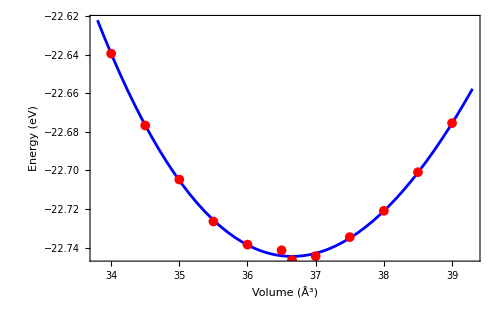

```mathematica
Plot[nlm[v],{v,(cellfm[[All,1]]//Min)-0.2,(cellfm[[All,1]]//Max)-0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cellfm]}
]
```

```mathematica
Clear[B0]
```

```mathematica
sol=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-4.46804,B0→-14.6426,v0→11.5807,B'→6.48705},{e0→-22.7445,B0→0.995559,v0→36.6534,B'→2.84629}}

```mathematica
Solve[v0==a0^3/4,a0]/.sol
```

{{{a0→-1.79571+3.11025 ⅈ},{a0→3.59141},{a0→-1.79571-3.11025 ⅈ}},{{a0→-2.6365+4.56655 ⅈ},{a0→5.273},{a0→-2.6365-4.56655 ⅈ}}}

### The antiferromagnetic AFM phase

```mathematica
cellafm=Import["cell-afm.dat"][[All,{1,2}]]
```

{{34.,-23.116},{34.5,-23.1638},{35.,-23.2},{35.5,-23.2257},{36.,-23.2414},{36.5,-23.2481},{37.,-23.2462},{37.5,-23.2366},{38.,-23.2196},{38.5,-23.1959},{39.,-23.166},{39.5,-23.1303},{40.,-23.0892},{36.6371,-23.2483}}

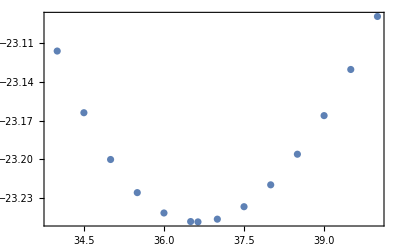

```mathematica
cellafm//ListPlot[#,Frame->True]&
```

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
```

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm=NonlinearModelFit[cellafm,model,parameters,v]
```

FittedModel[12.4702+19218./v^2+861.973/v^(4/3)-630.087/v^(2/3)]

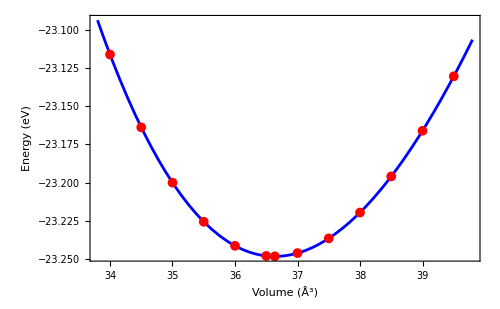

```mathematica
Plot[nlm[v],{v,(cellafm[[All,1]]//Min)-0.2,(cellafm[[All,1]]//Max)-0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cellafm]}
]
```

```mathematica
Clear[B0]
```

```mathematica
sol=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-23.2484,B0→1.21397,v0→36.6371,B'→4.57228}}

```mathematica
Solve[v0==a0^3/4,a0]/.sol
```

{{{a0→-2.63611+4.56588 ⅈ},{a0→5.27222},{a0→-2.63611-4.56588 ⅈ}}}

### DOS NM

```mathematica
input=Import["DOSCAR-nm","Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

5.74295

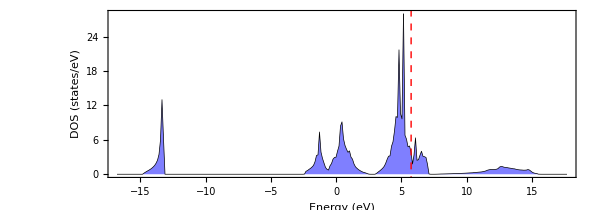

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->600,
PlotRange->{All,{0,28}},
AspectRatio->0.35]
```

### DOS FM

```mathematica
input=Import["DOSCAR-fm","Table"];
```

```mathematica
dosUP=input[[7;;7+300]][[All,{1,2}]];
dosDWN=input[[7;;7+300]][[All,{1,3}]]//Map[#{1,-1}&,#]&;
```

```mathematica
ef=input[[6,4]]
```

5.57746

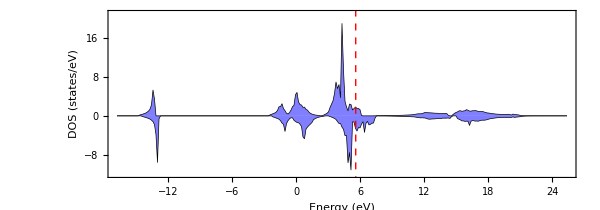

```mathematica
ListPlot[{dosUP,dosDWN},
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{{AbsoluteThickness[0.5],Black},{AbsoluteThickness[0.5],Black}},
ImageSize->600,
PlotRange->{All,{-12,21}},
AspectRatio->0.35]
```

### DOS AFM

```mathematica
input=Import["DOSCAR-afm","Table"];
```

```mathematica
dosUP=input[[7;;7+300]][[All,{1,2}]];
dosDWN=input[[7;;7+300]][[All,{1,3}]]//Map[#{1,-1}&,#]&;
```

```mathematica
ef=input[[6,4]]
```

5.17549

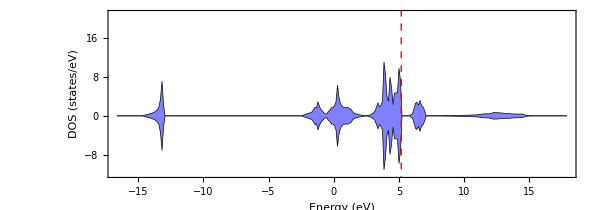

```mathematica
ListPlot[{dosUP,dosDWN},
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{{AbsoluteThickness[0.5],Black},{AbsoluteThickness[0.5],Black}},
ImageSize->600,
PlotRange->{All,{-12,21}},
AspectRatio->0.35]
```

## Part 8: The Si(100) surface

```mathematica
wrkdir=
"C:\\Users\\LeDar\\wrk\\dft2024\\part8_si100";
SetDirectory[wrkdir];
```

```mathematica
bulk=Import["POSCAR-bulk","Table"];
```

```mathematica
lattbulk=bulk[[2,1]]bulk[[3;;5]]
```

{{2.73444,2.73444,0.},{0.,2.73444,2.73444},{2.73444,0.,2.73444}}

```mathematica
{a,b,c}=lattbulk;
Δk=Table[0.07-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&,#]&//TableForm
```

0.07 | 5 | 5 | 5
0.065 | 5 | 5 | 5
0.06 | 5 | 5 | 5
0.055 | 6 | 6 | 6
0.05 | 6 | 6 | 6
0.045 | 7 | 7 | 7
0.04 | 8 | 8 | 8
0.035 | 9 | 9 | 9
0.03 | 11 | 11 | 11
0.025 | 13 | 13 | 13
0.02 | 16 | 16 | 16

```mathematica
bulk=Import["POSCAR-bulk","Table"];
```

```mathematica
lattbulk=bulk[[2,1]]bulk[[3;;5]]
```

{{2.73444,2.73444,0.},{0.,2.73444,2.73444},{2.73444,0.,2.73444}}

```mathematica
{a,b,c}=lattbulk;
Δk=Table[0.07-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&,#]&//TableForm
```

0.07 | 5 | 5 | 5
0.065 | 5 | 5 | 5
0.06 | 5 | 5 | 5
0.055 | 6 | 6 | 6
0.05 | 6 | 6 | 6
0.045 | 7 | 7 | 7
0.04 | 8 | 8 | 8
0.035 | 9 | 9 | 9
0.03 | 11 | 11 | 11
0.025 | 13 | 13 | 13
0.02 | 16 | 16 | 16

```mathematica
slab=Import["POSCAR-100","Table"];
```

```mathematica
lattslab=slab[[2,1]]slab[[3;;5]]
```

{{3.8671,0.,0.},{0.,3.8671,0.},{0.,0.,15.4689}}

```mathematica
{a,b,c}=lattslab;
Δk=Table[0.07-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&,#]&//TableForm
```

0.07 | 4 | 4 | 1
0.065 | 4 | 4 | 1
0.06 | 4 | 4 | 1
0.055 | 5 | 5 | 1
0.05 | 5 | 5 | 1
0.045 | 6 | 6 | 1
0.04 | 6 | 6 | 2
0.035 | 7 | 7 | 2
0.03 | 9 | 9 | 2
0.025 | 10 | 10 | 3
0.02 | 13 | 13 | 3

```mathematica
slab=Import["POSCAR-1x2l5v10-init.POSCAR","Table"];
```

```mathematica
lattslab=slab[[2,1]]slab[[3;;5]]
```

{{3.8671,0.,0.},{0.,7.7342,0.},{0.,0.,16.4689}}

```mathematica
{a,b,c}=lattslab;
Δk=Table[0.07-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&,#]&//TableForm
```

0.07 | 4 | 2 | 1
0.065 | 4 | 2 | 1
0.06 | 4 | 2 | 1
0.055 | 5 | 2 | 1
0.05 | 5 | 3 | 1
0.045 | 6 | 3 | 1
0.04 | 6 | 3 | 2
0.035 | 7 | 4 | 2
0.03 | 9 | 4 | 2
0.025 | 10 | 5 | 2
0.02 | 13 | 6 | 3

### Change of the energy per atom VS vacuum size

```mathematica
vac=Import["vacuum.dat"]//Map[#/{1,5}&,#]&
```

{{5.,-4.64607},{6.,-4.64016},{7.,-4.63912},{8.,-4.63821},{9.,-4.63788},{10.,-4.63788},{11.,-4.63828},{12.,-4.63773},{13.,-4.63768},{14.,-4.63756},{15.,-4.6376}}

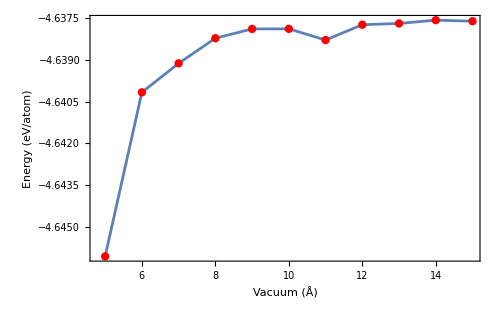

```mathematica
vac//ListPlot[#,
Frame->True,
FrameLabel->{"Vacuum (Å)","Energy (eV/atom)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
Joined->True,
ImageSize->500,
PlotRange->All,
Epilog->{Red,AbsolutePointSize[6],
Point[#]}
]&
```

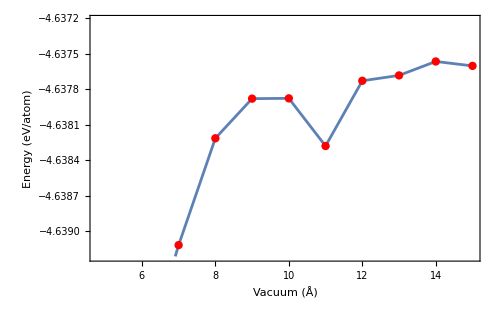

```mathematica
vac//ListPlot[#,
Frame->True,
FrameLabel->{"Vacuum (Å)","Energy (eV/atom)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
Joined->True,
ImageSize->500,
PlotRange->{-4.638214768-10^-3,-4.638214768+10^-3},
PlotRange->All,
Epilog->{Red,AbsolutePointSize[6],
Point[#]}
]&
```

### Surface energies

```mathematica
surfen=Import["surfaces.dat"][[All,{1,2}]];
surfen//TableForm
```

1x1l5v10 | -31.3996
1x2l5v10 | -62.7988
1x2l5v10b | -64.2757
1x2l5v10c | -64.4491
2x2l5v10 | -129.04

To compute the surface energy, we use:

```mathematica
A1x1=3.8671^2;
A1x2=3.8671 7.7342;
A2x2=7.7342^2;
```

```mathematica
e[Si]=-5.4240;
e[h]=-3.3795;
```

```mathematica
area={A1x1,A1x2,A1x2,A1x2,A2x2};
```

```mathematica
nsi={5,10,10,10,20};
nh={2,4,4,4,8};
```

```mathematica
results=Table[{surfen[[i,1]],area[[i]]//NumberForm[#,{4,2}]&,10^3 1/(2 area[[i]])(surfen[[i,2]]-nsi[[i]]e[Si]-nh[[i]]e[h])//NumberForm[#,{4,2}]&},{i,5}]
```

{{1x1l5v10,14.95,82.90},{1x2l5v10,29.91,82.90},{1x2l5v10b,29.91,58.22},{1x2l5v10c,29.91,55.32},{2x2l5v10,59.82,54.13}}

```mathematica
Join[{{"Slab","A (Å^2)","E_sf(meV/Å^2)"}},
results]//TableForm
```

Slab | A (Å^2) | E_sf(meV/Å^2)
1x1l5v10 | 14.95 | 82.90
1x2l5v10 | 29.91 | 82.90
1x2l5v10b | 29.91 | 58.22
1x2l5v10c | 29.91 | 55.32
2x2l5v10 | 59.82 | 54.13

### DOS of Si(100) surfaces

```mathematica
input1x1=Import["DOSCAR-1x1l5v10.st","Table"];
```

```mathematica
dos1x1=input1x1[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input1x1[[6,4]]
```

-0.579881

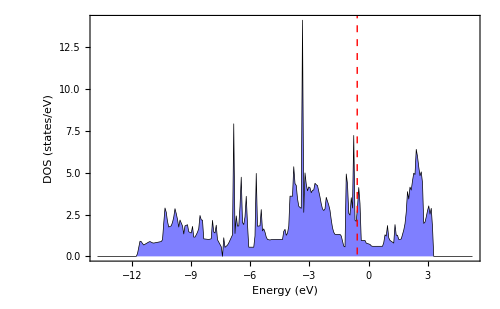

```mathematica
ListPlot[dos1x1,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All]
```

```mathematica
input1x2=Import["DOSCAR-1x2l5v10.st","Table"];
```

```mathematica
dos1x2=input1x2[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input1x2[[6,4]]
```

-0.124923

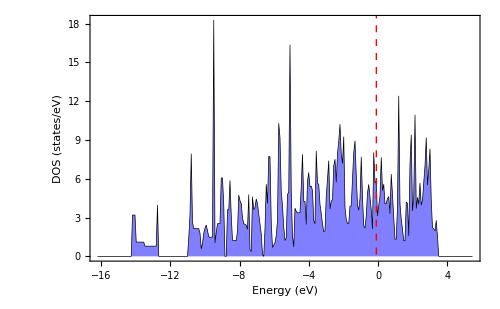

```mathematica
ListPlot[dos1x2,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All]
```

```mathematica
input1x2b=Import["DOSCAR-1x2l5v10b.st","Table"];
```

```mathematica
dos1x2b=input1x2b[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input1x2b[[6,4]]
```

-0.140672

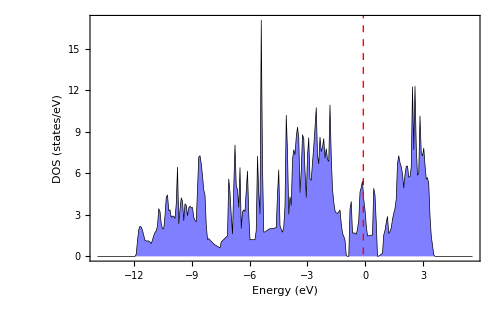

```mathematica
ListPlot[dos1x2b,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All]
```

```mathematica
input1x2c=Import["DOSCAR-1x2l5v10c.st","Table"];
```

```mathematica
dos1x2c=input1x2c[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input1x2c[[6,4]]
```

-0.415033

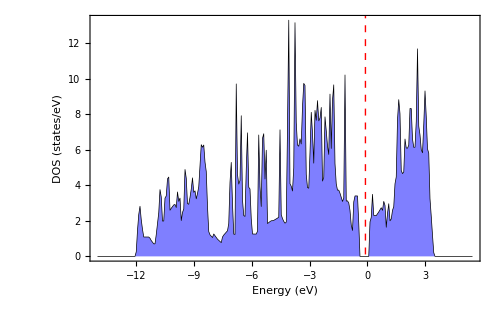

```mathematica
ListPlot[dos1x2c,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All]
```

```mathematica
input2x2=Import["DOSCAR-2x2l5v10.st","Table"];
```

```mathematica
dos2x2=input2x2[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input2x2[[6,4]]
```

-0.100115

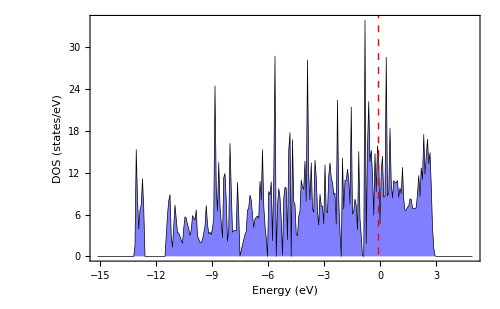

```mathematica
ListPlot[dos2x2,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All]
```

### Generation of STM images for SI (100)-2×2

```mathematica
wrkdir="/home/jdiego/Documentos/DFT/part8_si100/part8_si100";
SetDirectory[wrkdir];
```

```mathematica
in = Import["PARCHG-2x2l5v10.vasp", "Table"];
```

```mathematica
numat = Plus @@in[[7]]
```

28

```mathematica
thelattice = in [[3;;5]]
```

{{7.7342,0.,0.},{0.,7.7342,0.},{0.,0.,16.4689}}

```mathematica
in[[ 7 + numat + 3]]
```

{80,80,168}

```mathematica
stm = (in[[ 7 + numat+4;; -1]]//Flatten);
```

```mathematica
stm//Dimensions
```

{1075200}

```mathematica
stm[[-1]]
```

0.49454

```mathematica
divX = in[[7 + numat +3 , 1 ]]
```

80

```mathematica
divY= in[[7 + numat +3 , 2 ]]
```

80

```mathematica
zrange = in[[5 , {2,3}]]
```

{0.,16.4689}

```mathematica
transformDATA =
(
#
 //Partition[# , divX]&
  //Partition[# , divY]&
//Map[Append[#,First[#]]&,
#,{2}]&
//Map[Append[#,First[#]]&,#]&
//Transpose[# ,{3,2,1}]&

)&;
```

```mathematica
stm1= stm//transformDATA;
```

```mathematica
stm1[[1,1]][[1]]
```

0.5083

```mathematica
stm1//Dimensions
```

{81,81,168}

### Here the interpolation for stm1

```mathematica
theInterplation = ListInterpolation[#,{{0 , in[[3,1]]},{0, in[[4,2]]},{0,in[[5,3]]}},PeriodicInterpolation->{True, True , False}]&;
```

```mathematica
stminterpolation = stm1//theInterplation;
```

```mathematica
stminterpolation[0,0,3]
```

74.4898

```mathematica
nx = 2;
ny=2;

ContourPlot3D[stminterpolation[x,y,z]==0.049,
{x,0,nx thelattice[[1,1]]},
{y,0, ny thelattice[[2,2]]},
{z , 8.6,11.6},
ColorFunction->Function[{x,y,z,f},
ColorData["SunsetColors"][z]],
PlotPoints->30,
MaxRecursion->0,
BoxRatios->{1,(ny thelattice[[2,2]])/(nx thelattice[[1,1]]), (11.6-8.6)/(nx thelattice[[1,1]])},
AxesLabel->{"x(A)","y(A)", None},
ViewPoint->{0,0,∞},
BaseStyle->{FontFamily->"Helvetica",FontSize->13}, 
ContourStyle->Directive[Opacity[1.]], 
Lighting->AmbientLight[GrayLevel[1.]], 
Mesh->None]
```

-Graphics3D-

```mathematica
nx = 1;
ny=4;

ContourPlot3D[stminterpolation[x,y,z]==0.08,
{x,0,nx thelattice[[1,1]]},
{y,0, ny thelattice[[2,2]]},
{z , 8.6,11.6},
ColorFunction->Function[{x,y,z,f},
ColorData["SunsetColors"][z]],
PlotPoints->40,
MaxRecursion->0,
BoxRatios->{1,(ny thelattice[[2,2]])/(nx thelattice[[1,1]]), (11.6-8.6)/(nx thelattice[[1,1]])},
AxesLabel->{"x(A)","y(A)", None},
ViewPoint->{0,0,∞},
BaseStyle->{FontFamily->"Helvetica",FontSize->13}, 
ContourStyle->Directive[Opacity[1.]], 
Lighting->AmbientLight[GrayLevel[1.]], 
Mesh->None]
```

-Graphics3D-

```mathematica
nx = 2;
ny=2;

ContourPlot3D[stminterpolation[x,y,z]==0.08,
{x,0,nx thelattice[[1,1]]},
{y,0, ny thelattice[[2,2]]},
{z , 8.6,11.6},
ColorFunction->Function[{x,y,z,f},
ColorData["SunsetColors"][z]],
PlotPoints->80,
MaxRecursion->0,
BoxRatios->{1,(ny thelattice[[2,2]])/(nx thelattice[[1,1]]), (11.6-8.6)/(nx thelattice[[1,1]])},
AxesLabel->{"x(A)","y(A)", None},
Axes-> {True ,True , False},
ViewPoint->{0,0,∞},
BaseStyle->{FontFamily->"Helvetica",FontSize->13}, 
ContourStyle->Directive[Opacity[1.]], 
Lighting->AmbientLight[GrayLevel[1.]],
ImageSize->600, 
Mesh->None]
```

-Graphics3D-

```mathematica
nx = 3;
ny=4;

RegionPlot3D[stminterpolation[x,y,z]>=0.08,
{x,0,nx thelattice[[1,1]]},
{y,0, ny thelattice[[2,2]]},
{z , 8.6,11.6},
ColorFunction->ColorData["SunsetColors"],
PlotPoints->40,
MaxRecursion->0,
BoxRatios->{1,(ny thelattice[[2,2]])/(nx thelattice[[1,1]]), (11.6-8.6)/(nx thelattice[[1,1]])},
AxesLabel->{"x(A)","y(A)", "z(A)"},
Axes-> {True ,True , True},
BaseStyle->{FontFamily->"Helvetica",FontSize->13}, 
Lighting->AmbientLight[GrayLevel[1.]],
ImageSize->600, 
Mesh->None,
PlotLegends->Automatic]
```

-Graphics3D-